```mathematica
Manipulate[
Module[{L,T},
L=4;T=0.5;If[LF>#,LF=#]&@(4-T/Tan[θ]);

Graphics[{
(*{Thick,Dashed,Purple,Line[{{4,-2},{4,6}}],Line[{{4,-2},{6,-2}}]},*)
(*{Red,Line[{{0,0},{L*Cos[θ],L*Sin[θ]}}]},
{Green,Line[{{-T*Sin[θ],T*Cos[θ]},{L*Cos[θ]-T*Sin[θ],L*Sin[θ]+T*Cos[θ]}}]},*)
{Red,Arrow[{{-T*Sin[θ]+T*Tan[θ/2],T*Cos[θ]-T},{L*Cos[θ],L*Sin[θ]}}],
Point[{-T*Sin[θ]+T*Tan[θ/2],T*Cos[θ]-T}],
(*Text[Style[#,16,Background->White],#,{1,1}]&@{-T*Sin[θ]+T*Tan[θ/2],T*Cos[θ]-T}*)
},
{Green,Arrow[{{-T*Sin[θ],T*Cos[θ]},{L*Cos[θ]-(T*Sin[θ/2]),L*Sin[θ]+T}}]},

(*Line[{{L*Cos[θ],L*Sin[θ]},{L*Cos[θ]+0.75,L*Sin[θ]}}],
Line[{{L*Cos[θ],L*Sin[θ]+T},{L*Cos[θ]+0.75,L*Sin[θ]+T}}],*)
Red,
Line[{{-T*Sin[θ],T*Cos[θ]},{-T*Sin[θ]-0.75,T*Cos[θ]}}],
Black,
Line[{{-T*Sin[θ],T*Cos[θ]-T},{-T*Sin[θ]-.75-T,T*Cos[θ]-T}}],
Line[{{-T*Sin[θ]-0.75-T,T*Cos[θ]-T},{-T*Sin[θ]-0.75-T,T*Cos[θ]-T+0.75+T}}],Line[{{-T*Sin[θ]-0.75,T*Cos[θ]},{-T*Sin[θ]-0.75,T*Cos[θ]+0.75+T}}],
(*Line[{{-T*Sin[θ]-0.75,T*Cos[θ]+0.75+T},{-T*Sin[θ]-0.75-(0.5+T),T*Cos[θ]+0.75+T}}],
Line[{{-T*Sin[θ]-0.75-T,T*Cos[θ]-T+0.75+T},{-T*Sin[θ]-0.75-T-0.5,T*Cos[θ]-T+0.75+T}}],*)

(*{Thick,Orange,
Line[{(*{-T*Sin[θ],T*Cos[θ]-T},*){-T*Sin[θ]+(T*Tan[θ/2]),T*Cos[θ]-T},{0,0}}],
Line[{(*{L*Cos[θ]-T*Sin[θ],L*Sin[θ]+T*Cos[θ]},*){L*Cos[θ]-(T*Sin[θ/2]),L*Sin[θ]+T},{L*Cos[θ],L*Sin[θ]+T}}]},*)

Circle[{L*Cos[θ]+0.75+((T/2)*Tan[45]),L*Sin[θ]+(T/2)},((T/2)/Cos[45]),{-3.3Pi/4,3.3Pi/4}],
Circle[{-T*Sin[θ]-0.75-((T/2)*Tan[45])-(0.5+T),T*Cos[θ]-(T/2)+(0.75+T)},((T/2)/Cos[45]),{7.3Pi/4,0.7Pi/4}],

{Hue[0.5,1,1,0.4],Polygon[{
{-T*Sin[θ]-0.75-T,T*Cos[θ]+T/2},{-T*Sin[θ]-0.75,T*Cos[θ]+T/2},{-T*Sin[θ]-0.75,T*Cos[θ]},
{-T*Sin[θ],T*Cos[θ]},
{-T*Sin[θ]+(LF*Cos[θ]),T*Cos[θ]+(LF*Sin[θ])},

{-T*Sin[θ]+(LF*Cos[θ])+((T/Cos[θ])/Tan[θ]),
T*Cos[θ]+(LF*Sin[θ])},
{-T*Sin[θ]+(T*Tan[θ/2]),
T*Cos[θ]-T},
{-T*Sin[θ]-.75-T,T*Cos[θ]-T}
}]},

{Thick,
Line[{{-T*Sin[θ]+(T*Tan[θ/2])+0.1*Sin[θ],
T*Cos[θ]-T-0.1*Cos[θ]},{-T*Sin[θ]+(T*Tan[θ/2])+0.3*Sin[θ],
T*Cos[θ]-T-0.3*Cos[θ]}}],
Line[{{-T*Sin[θ]+(LF*Cos[θ])+((T/Cos[θ])/Tan[θ])+0.1*Sin[θ],
T*Cos[θ]+(LF*Sin[θ])-0.1*Cos[θ]},{-T*Sin[θ]+(LF*Cos[θ])+((T/Cos[θ])/Tan[θ])+0.3*Sin[θ],
T*Cos[θ]+(LF*Sin[θ])-0.3*Cos[θ]}}],
Line[{{-T*Sin[θ]+(T*Tan[θ/2])+0.2*Sin[θ],
T*Cos[θ]-T-0.2*Cos[θ]},{-T*Sin[θ]+(LF*Cos[θ])+((T/Cos[θ])/Tan[θ])+0.2*Sin[θ],
T*Cos[θ]+(LF*Sin[θ])-0.2*Cos[θ]}}]},

Text[Style[Style["L",16],13],{((-T*Sin[θ]+(LF*Cos[θ])+((T/Cos[θ])/Tan[θ])+0.3*Sin[θ])+(-T*Sin[θ]+(LF*Cos[θ])+((T/Cos[θ])/Tan[θ])+0.3*Sin[θ]))/4+1,((T*Cos[θ]+(LF*Sin[θ])-0.3*Cos[θ])+(T*Cos[θ]-T-0.3*Cos[θ]))/4}],
Text[Style["B",16],{L*Cos[θ]+0.75+((T/2)*Tan[45]),L*Sin[θ]+(T/2)}],
Text[Style["A",16],{-T*Sin[θ]-0.75-((T/2)*Tan[45])-(0.5+T),T*Cos[θ]-(T/2)+(0.75+T)}]
},ImageSize->{500,300},Frame->True,PlotRange->{{-3.2,5.5},{-0.55,3.9}},
(*PlotLabel->{√((L*Cos[θ]-(-T*Sin[θ]+T*Tan[θ/2]))^2+(L*Sin[θ]-(T*Cos[θ]-T))^2),√((L*Cos[θ]-(T*Sin[θ/2])-(-T*Sin[θ]))^2+(L*Sin[θ]+T-T*Cos[θ])^2)}*)
PlotLabel->{{√(Abs[L*Cos[θ]-(-T*Sin[θ]+T*Tan[θ/2])]^2+Abs[L*Sin[θ]-(T*Cos[θ]-T)]^2),√(Abs[L*Cos[θ]-(T*Sin[θ/2])-(-T*Sin[θ])]^2+Abs[L*Sin[θ]+T-T*Cos[θ]]^2)},{-T*Sin[θ]+T*Tan[θ/2],T*Cos[θ]-T}}]
],
Control[{{θ,25 °,"angle"},20 °,50 °,1°,Appearance->"Labeled"}],
Control[{{LF,1.5,"fluid length"},0,4,Appearance->"Labeled"}]
]
```

```mathematica
PlotRange->{{-3.2,5.5},{-0.55,3.9}}
```

```mathematica
{White,Line[{{4,-2},{4,6}}],Line[{{4,-2},{6,-2}}]},
```

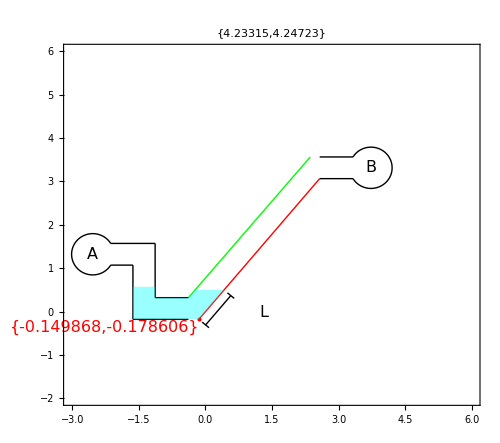
```mathematica
ImageDimensions@-Graphics-
```

{500,463}

```mathematica
1.45-0.7
```

0.75

```mathematica
1.45/0.75
```

1.93333

```mathematica
{{-T*Sin[θ]+T*Tan[θ/2],T*Cos[θ]-T},{L*Cos[θ],L*Sin[θ]}}
```

```mathematica
√((L*Cos[θ]-(-T*Sin[θ]+T*Tan[θ/2]))^2+(L*Sin[θ]-(T*Cos[θ]-T))^2)
```

```mathematica
{{-T*Sin[θ],T*Cos[θ]},{L*Cos[θ]-(T*Sin[θ/2]),L*Sin[θ]+T}}
```

```mathematica
√((L*Cos[θ]-(T*Sin[θ/2])-(-T*Sin[θ]))^2+(L*Sin[θ]+T-T*Cos[θ])^2)
```